## Start

```mathematica
Clear["`*"]
e=1.6*10^-19;kB=1.38*10^-23;dens=10^19;temp=10^3*e/kB;pres0=kB dens*temp;μ0=1.25663706212*10^-6;
folder=NotebookDirectory[];
shot="54719";
shot="77651";
shot="68408";
folderdata=folder<>shot;
SetDirectory[folderdata];
files=FileNames["*.dat"]⟦1;;1⟧;
data4=Table[Flatten[Import[files⟦i⟧]],{i,Length[files]}];
(*assesing information from imported data*)
np=129;{RDIM,ZDIM,RCENTR,RLEFT,ZMID,RMAXIS,ZMAXIS,SIMAG,SIBRY,BCENTR,CURRENT,psi0,a1,a2,a3,a4,a5,a6,a7,a8}=Transpose[data4⟦All,1;;20⟧];
factorscal=1;
{SIMAG,SIBRY}=factorscal{SIMAG,SIBRY};
```

```mathematica
SIMAG
SIBRY
```

{-0.0483252}

{0.}

## Build quantities: grid and on-the-grid

```mathematica
(*R-Z grid*)
δR=Table[RDIM⟦i⟧-0RLEFT[[i]],{i,Length[data4]}]/(np-1);δZ=Table[ZDIM⟦i⟧,{i,Length[data4]}]/(np-1);R=Table[Table[RLEFT⟦i⟧+δR⟦i⟧ (Range[np]-1),{j,np}]//Transpose,{i,Length[data4]}];
Z=Table[Table[(2 Range[np]-np-1)/2 δZ⟦i⟧,{j,np}],{i,Length[data4]}];
(*F,P,F',P'*)
FPOL=data4⟦All,20+0 np+1;;20+1 np⟧;
PRES=data4⟦All,20+1 np+1;;20+2 np⟧;
FFPRIM=factorscal data4⟦All,20+2 np+1;;20+3 np⟧;
PPRIME=factorscal data4⟦All,20+3 np+1;;20+4 np⟧;
(*q,ψ,∂_R ψ,∂_Z ψ,∂_RR ψ,∂_RZ ψ,∂_ZZ ψ*)
Q=data4⟦All,20+(np+4) np+1;;20+(np+5) np⟧;
PSI=factorscal Table[ArrayReshape[data4⟦i,20+4 np+1;;20+(np+4) np⟧,{np,np}]//Transpose,{i,Length[data4]}];
PSIR=Table[(RotateLeft[PSI⟦i⟧,{1,0}]-RotateLeft[PSI⟦i⟧,{-1,0}])/(2δR[[i]]),{i,Length[data4]}];
PSIZ=Table[(RotateLeft[PSI⟦i⟧,{0,1}]-RotateLeft[PSI⟦i⟧,{0,-1}])/(2δZ[[i]]),{i,Length[data4]}];
PSIRR=Table[(RotateLeft[PSIR⟦i⟧,{1,0}]-RotateLeft[PSIR⟦i⟧,{-1,0}])/(2δR[[i]]),{i,Length[data4]}];
PSIRZ=Table[(RotateLeft[PSIR⟦i⟧,{0,1}]-RotateLeft[PSIR⟦i⟧,{0,-1}])/(2δZ[[i]]),{i,Length[data4]}];
PSIZZ=Table[(RotateLeft[PSIZ⟦i⟧,{0,1}]-RotateLeft[PSIZ⟦i⟧,{0,-1}])/(2δZ[[i]]),{i,Length[data4]}];
(*plasma boundary*)
{nbbbs,limitr}=data4[[All,20+(np+5)np+1;;20+(np+5)np+2]]//Transpose;
rbound=Table[data4[[as,23+(np+5)np;;22+(np+5)np+2nbbbs[[as]]]],{as,Length[data4]}];
zbound=Table[rbound[[as,2i]],{as,Length[data4]},{i,nbbbs[[as]]}];
rbound=Table[rbound[[as,2i-1]],{as,Length[data4]},{i,nbbbs[[as]]}];
(*rlim=Table[data4[[as,23+(np+5)np+2nbbbs[[as]];;22+(np+5)np+2nbbbs[[as]]+2limitr[[as]]]],{as,Length[data4]}];
zlim=Table[rlim[[as,2i]],{as,Length[data4]},{i,limitr[[as]]}];
rlim=Table[rlim[[as,2i-1]],{as,Length[data4]},{i,limitr[[as]]}];*)
(*magnetic axis position and field*)
R0=RMAXIS;
B0=FPOL[[All,1]]/RMAXIS;
(*Evaluating F(ψ) on the R-Z grid*)
ℱ=Φt=ρ=Range[Length[data4]];
Monitor[For[as=1,as≤Length[data4],as++,npp=np;Δ=(SIBRY⟦as⟧-SIMAG⟦as⟧)/(npp-1);ψ=SIMAG⟦as⟧+Δ (Range[npp]-1);F=Interpolation[Transpose[{ψ,FPOL⟦as⟧}]];ℱ⟦as⟧=F[PSI⟦as⟧];
Φt[[as]]=Table[Total[ℱ⟦as⟧/R[[as]] HeavisideTheta[Max[ψ⟦j⟧,SIMAG[[as]]]-PSI⟦as⟧]HeavisideTheta[-Min[ψ⟦j⟧,SIMAG[[as]]]+PSI⟦as⟧] δR⟦as⟧ δZ⟦as⟧,2],{j,Length[ψ]}];
Φt⟦as⟧=Φt⟦as⟧/Φt⟦as,Length[ψ]⟧//Sqrt;
Fρ=Interpolation[Transpose[{ψ,Φt⟦as⟧}]];
ρ⟦as⟧=Fρ[PSI⟦as⟧];
];,{as}]
ρR=Table[(RotateLeft[ρ⟦i⟧,{1,0}]-RotateLeft[ρ⟦i⟧,{-1,0}])/(2δR[[i]]),{i,Length[data4]}];
ρZ=Table[(RotateLeft[ρ⟦i⟧,{0,1}]-RotateLeft[ρ⟦i⟧,{0,-1}])/(2δZ[[i]]),{i,Length[data4]}];

(*Evaluating Subscript[q, θ](ψ,θ) on the R-Z grid*)
qθ=-Table[(((R⟦as⟧-RMAXIS⟦as⟧)^2+(Z⟦as⟧-ZMAXIS[[as]])^2) ℱ⟦as⟧)/(R⟦as⟧ (Z⟦as⟧-ZMAXIS[[as]]) PSIZ⟦as⟧+R⟦as⟧ (R⟦as⟧-RMAXIS⟦as⟧) PSIR⟦as⟧),{as,Length[data4]}];

(*Estimate triangulation, geoemtrical center, *){Rmax,Rmin,Zmax,Rsup}=Table[{Max[rbound⟦as⟧],Min[rbound⟦as⟧],Max[zbound⟦as⟧],rbound⟦as,1⟧},{as,Length[data4]}]//Transpose;
{a,Rgeo}={(Rmax-Rmin)/2,(Rmax+Rmin)/2};
{δ,κ}={(Rgeo-Rsup)/a,(2Zmax)/a/2};
```

InterpolatingFunction::dmval: Input value {0.00661798} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00643146} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00625367} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
raza=Table[√((R⟦as⟧-R0⟦as⟧)^2+Z⟦as⟧^2)+0.00,{as,Length[R]}];
```

```mathematica
{ListPlot[{raza⟦1,65,65;;129⟧,a⟦1⟧ ρ⟦1,65,65;;129⟧},PlotStyle->{Red,Blue}],
ListPlot3D[{raza⟦1⟧/a⟦1⟧,ρ⟦1⟧},PlotRange->{{30,100},{30,100},{0,1}},PlotStyle->{Red,Blue}]}
```

```mathematica
as=1;boundary=Transpose[{rbound⟦as⟧,zbound⟦as⟧}];
boundaryPolygon=Polygon[boundary];insideQ=RegionMember[boundaryPolygon];
points=Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[ρ⟦as⟧]}];
filteredPoints=Select[points,insideQ[{#1⟦1⟧,#1⟦2⟧}]&];
points=Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[raza⟦as⟧/a[[as]]]}];
filteredPoints2=Select[points,insideQ[{#1⟦1⟧,#1⟦2⟧}]&];
ListPlot3D[{filteredPoints,filteredPoints2},PlotRange->All]
```

-Graphics3D-

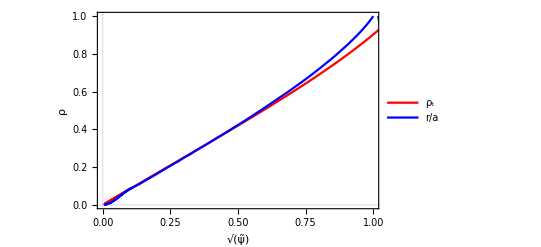

```mathematica
ListLinePlot[{Transpose[{((PSI⟦1,65;;np,65⟧-SIMAG⟦1⟧)/(SIBRY⟦1⟧-SIMAG⟦1⟧))//Sqrt,raza⟦1,65;;np,65⟧/a⟦1⟧}],Transpose[{((PSI⟦1,65;;np,65⟧-SIMAG⟦1⟧)/(SIBRY⟦1⟧-SIMAG⟦1⟧))//Sqrt, ρ⟦1,65;;np,65⟧}]},PlotStyle->{Red,Blue},PlotRange->{{0,1},{0,1}},PlotTheme->"Scientific",LabelStyle->{Black,Bold,15},FrameLabel->{"√(ψ̃)","ρ"},PlotLegends->Placed[{"ρ_t","r/a"},{0.8,0.2}]]
```

```mathematica
(*Proof that RMAXIS is the real magnetic axis where ∇ψ=0*)
```

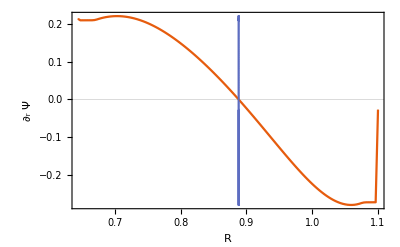
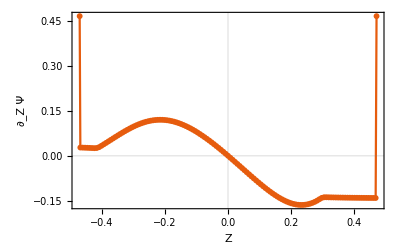

```mathematica
as=1;fas=(np-1)/2;
{ListLinePlot[{Transpose[{R⟦as,All,fas⟧,PSIR⟦as,All,fas⟧}],Transpose[{R⟦as,All,fas⟧ 0+RMAXIS⟦as⟧,PSIR⟦as,All,fas⟧}]},PlotMarkers->{Automatic,1},PlotTheme->"Scientific",FrameLabel->{"R","∂_r Ψ"},LabelStyle->{Black,Bold,10}],ListLinePlot[Transpose[{Z⟦as,fas⟧,PSIZ⟦as,fas⟧}],PlotMarkers->{Automatic,6},PlotTheme->"Scientific",FrameLabel->{"Z","∂_Z Ψ"},LabelStyle->{Black,Bold,10}]}
```

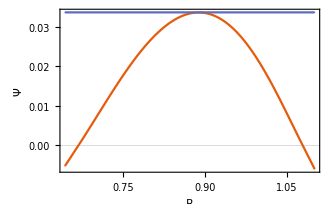
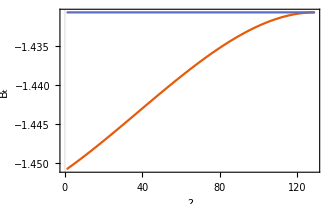

```mathematica
(*Proof that SIMAG is the poloidal flux at the magnetic axis*){ListLinePlot[{Transpose[{R⟦as,All,fas⟧,PSI⟦as,All,fas⟧}],Transpose[{R⟦as,All,fas⟧,SIMAG[[as]]+0PSI⟦as,All,fas⟧}]},PlotMarkers->{Automatic,1},PlotTheme->"Scientific",FrameLabel->{"R","Ψ"},LabelStyle->{Black,Bold,15},ImageSize->333],ListLinePlot[{FPOL[[as]]/RCENTR[[as]],BCENTR[[as]]+FPOL[[as]]0},PlotMarkers->{Automatic,1},PlotTheme->"Scientific",FrameLabel->{"?","B_t"},LabelStyle->{Black,Bold,15},ImageSize->333]}
```

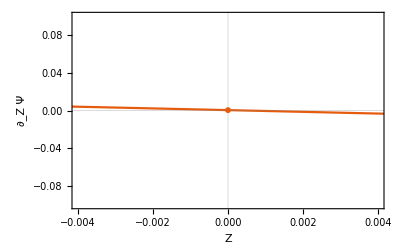

```mathematica
ListLinePlot[Transpose[{Z⟦as,fas⟧,PSIZ⟦as,fas⟧}],PlotRange->{.2{-0.02,0.02},{-0.1,0.1}},PlotMarkers->{Automatic,6},PlotTheme->"Scientific",FrameLabel->{"Z","∂_Z Ψ"},LabelStyle->{Black,Bold,10}]
```

```mathematica
(*Checking the poloidal flux grid*)
```

Power::infy: Infinite expression 1/0. encountered.

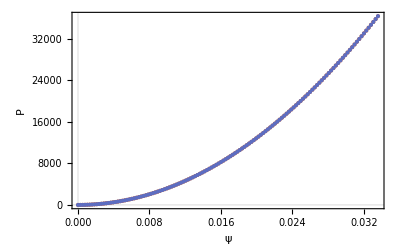
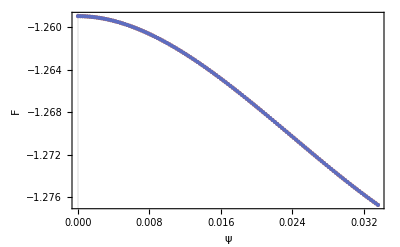
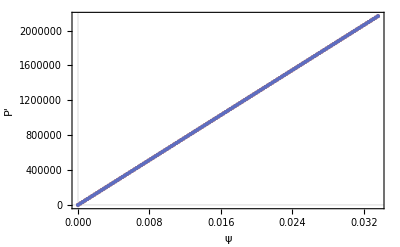
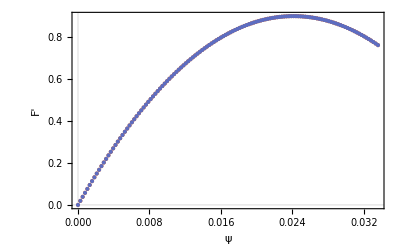
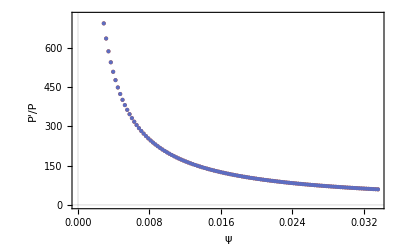

```mathematica
as=1;npp=np;Δ=(SIBRY⟦as⟧-SIMAG⟦as⟧)/(npp-1);ψ=SIMAG⟦as⟧+Δ (Range[npp]-1);
{q,P,F}={Interpolation[Transpose[{ψ,Q⟦as⟧}]],Interpolation[Transpose[{ψ,PRES⟦as⟧}]],Interpolation[Transpose[{ψ,FPOL⟦as⟧}]]};
{PP[x_],FF[x_]}={D[P[x], x],F[x] D[F[x], x]};
grafix[a_,b_,c_,d_]:=ListPlot[{Transpose[{ψ,a}],Transpose[{ψ,b}]},PlotTheme->"Scientific",FrameLabel->{c,d},LabelStyle->{Black,Bold,10}];
{grafix[PRES⟦as⟧,P[ψ],"ψ","P"],grafix[FPOL⟦as⟧,F[ψ],"ψ","F"],grafix[PPRIME⟦as⟧,PP[ψ],"ψ","P'"],grafix[FFPRIM⟦as⟧,FF[ψ],"ψ","F'"],grafix[PPRIME⟦as⟧/PRES[[as]],PP[ψ]/P[ψ],"ψ","P'/P"]}
```

```mathematica
(*Toroidal current*)
```

```mathematica
𝒥=Range[Length[R]];Monitor[For[as=1,as≤Length[R],as++,npp=np;Δ=(SIBRY⟦as⟧-SIMAG⟦as⟧)/(npp-1);ψ=SIMAG⟦as⟧+Δ (Range[npp]-1);{q,P,F}={Interpolation[Transpose[{ψ,Q⟦as⟧}]],Interpolation[Transpose[{ψ,PRES⟦as⟧}]],Interpolation[Transpose[{ψ,FPOL⟦as⟧}]]};{PP[x_],FF[x_]}={D[P[x], x],F[x] D[F[x], x]};𝒥⟦as⟧=(R⟦as⟧ PP[PSI⟦as⟧]+FF[PSI⟦as⟧]/(μ0 R⟦as⟧));],as]
```

InterpolatingFunction::dmval: Input value {0.00661798} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00643146} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00625367} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Table[(2 Max[Z⟦as⟧] (Max[R⟦as⟧]-Min[R⟦as⟧]))/Length[R⟦as⟧]^2 Total[HeavisideTheta[SIBRY⟦as⟧-PSI⟦as⟧] 𝒥⟦as⟧,2],{as,Length[R]}]/CURRENT
```

{-0.996643}

```mathematica
as=1;ListPlot3D[HeavisideTheta[SIBRY[[as]]-PSI[[as]]]𝒥⟦as⟧/10^5,PlotRange->{All,All,All}]
```

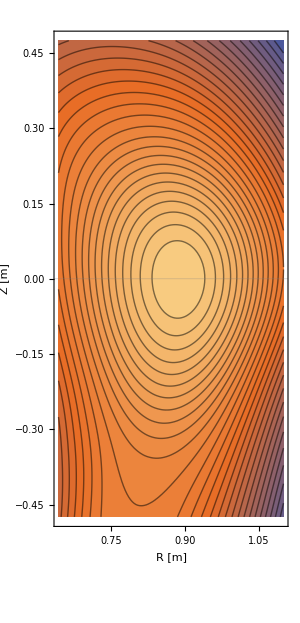
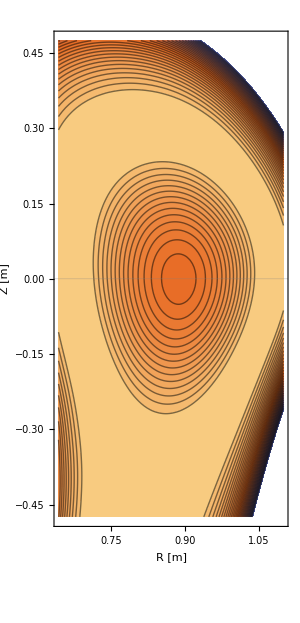

```mathematica
(*Plasma Boundary, tokamak volume, poloidal flux and F in contourplots*)as=1;grafs={ListContourPlot[Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[PSI⟦as⟧]}],Contours->30,AspectRatio->{Max[R⟦as⟧],2 Max[Z⟦as⟧]},PlotTheme->"Scientific",FrameLabel->{"R [m]","Z [m]","ψ"},LabelStyle->{Black,Bold,15},ImageSize->300],ListContourPlot[Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[ℱ⟦as⟧]}],Contours->30,AspectRatio->{Max[R⟦as⟧],2 Max[Z⟦as⟧]},PlotTheme->"Scientific",FrameLabel->{"R [m]","Z [m]","F[ψ]"},LabelStyle->{Black,Bold,15},ImageSize->300]}
```

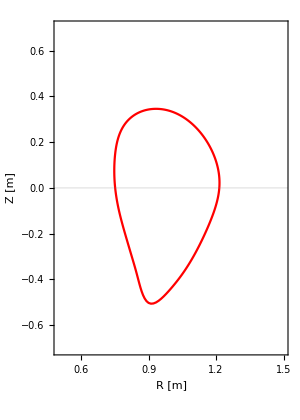

```mathematica
ListLinePlot[Transpose[{rbound⟦as⟧,zbound⟦as⟧}/R0⟦as⟧],PlotRange->{{0.5,1.5},{-(3 a⟦as⟧)/R0⟦as⟧,(3 a⟦as⟧)/R0⟦as⟧}},AspectRatio->{1.5 R0⟦as⟧,6 a⟦as⟧},PlotStyle->{Red},PlotTheme->"Scientific",FrameLabel->{"R [m]","Z [m]"},LabelStyle->{Black,Bold,15},ImageSize->300]
```

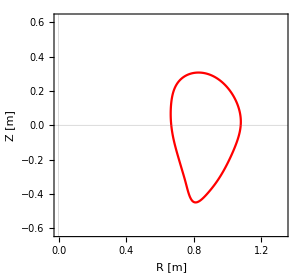
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Plasma Boundary, tokamak volume, poloidal flux and F in contourplots*)as=1;grafs={ListLinePlot[Transpose[{rbound⟦as⟧,zbound⟦as⟧}],PlotRange->{{0,1.5 R0[[as]]},{-3a[[as]],3a[[as]]}},AspectRatio->{1.5R0[[as]],6a[[as]]},PlotStyle->{Red},PlotTheme->"Scientific",FrameLabel->{"R [m]","Z [m]"},LabelStyle->{Black,Bold,15},ImageSize->300],ListContourPlot[Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[PSI⟦as⟧]}],Contours->30,AspectRatio->{Max[R⟦as⟧],2 Max[Z⟦as⟧]},PlotTheme->"Scientific",FrameLabel->{"R [m]","Z [m]","ψ"},LabelStyle->{Black,Bold,15},ImageSize->300],ListContourPlot[Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[ℱ⟦as⟧]}],Contours->30,AspectRatio->{Max[R⟦as⟧],2 Max[Z⟦as⟧]},PlotTheme->"Scientific",FrameLabel->{"R [m]","Z [m]","F[ψ]"},LabelStyle->{Black,Bold,15},ImageSize->300]}
```

## Exporting for χ ~ arctan(θ)

```mathematica
Monitor[For[as=1,as≤Length[R],as++,radius=4;order=4;Clear[fnc];{minR,maxR,minZ,maxZ}={Min[rbound⟦as⟧],Max[rbound⟦as⟧],Min[zbound⟦as⟧],Max[zbound⟦as⟧]};ngrid=150;ℛ=Transpose[Table[minR+((maxR-minR) (Range[ngrid]-1))/(ngrid-1),{j,ngrid}]];𝒵=Table[minZ+((maxZ-minZ) (Range[ngrid]-1))/(ngrid-1),{j,ngrid}];Ψ=Interpolation[Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[GaussianFilter[PSI⟦as⟧,radius]]}],InterpolationOrder->order,Method->"Spline"];Ρ=Interpolation[Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[GaussianFilter[ρ⟦as⟧,radius]]}],InterpolationOrder->order,Method->"Spline"];fnc[r_,z_]=Ψ[r,z];psihalf=fnc[RMAXIS⟦as⟧+a⟦as⟧/2,0];ψ0=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ψ[r,z], r];ψr=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ψ[r,z], z];ψz=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ψ[r,z], r,r];ψrr=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ψ[r,z], r,z];ψrz=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ψ[r,z], z,z];ψzz=fnc[ℛ,𝒵];fnc[r_,z_]=Ρ[r,z];ρint=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ρ[r,z], r];ρintR=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ρ[r,z], z];ρintZ=fnc[ℛ,𝒵];Δ=(SIBRY⟦as⟧-SIMAG⟦as⟧)/(npp-1);ψ=SIMAG⟦as⟧+Δ (Range[npp]-1);fnc=Interpolation[Transpose[{ψ,PRES⟦as⟧}],InterpolationOrder->order];pres=fnc[psihalf];fnc=Interpolation[Transpose[{ψ,PPRIME⟦as⟧}],InterpolationOrder->order];ppres=fnc[psihalf];fnc=Interpolation[Transpose[{ψ,FPOL⟦as⟧}],InterpolationOrder->order];ℱs=fnc[ψ0];fnc=Interpolation[Transpose[{ψ,FFPRIM⟦as⟧/FPOL⟦as⟧}],InterpolationOrder->order];Fψprim=fnc[ψ0];fnc=Interpolation[Transpose[{ψ,Q⟦as⟧}],InterpolationOrder->order];qψ=fnc[ψ0];fnc1=Interpolation[Transpose[{ψ,GaussianFilter[Φt⟦as⟧,radius]}],InterpolationOrder->order];fnc2=Interpolation[Transpose[{ψ,GaussianFilter[Q⟦as⟧,radius]}],InterpolationOrder->order];g3[z3_]=D[fnc2[z3], z3]/D[fnc1[z3], z3];qprim=g3[ψ0];MHD={Flatten[ψ0],Flatten[ψr],Flatten[ψz],Flatten[ψrr],Flatten[ψrz],Flatten[ψzz],Flatten[ℱs],Flatten[Fψprim],Flatten[qψ],Flatten[qprim],Flatten[ρint],Flatten[ρintR],Flatten[ρintZ]};Nqua=Length[MHD];QQ=Flatten[{R0⟦as⟧,B0⟦as⟧,ngrid,ngrid,minR,maxR,minZ,maxZ,a⟦as⟧,δ⟦as⟧,κ⟦as⟧,Nqua}];For[jai=1,jai≤Nqua,jai++,QQ=Append[QQ,MHD⟦jai⟧];];Export[folderdata<>"\\QQ_"<>StringTake[files⟦as⟧,-5],QQ//Flatten];],as]
```

InterpolatingFunction::dmval: Input value {0.00436561} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00419131} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00401782} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
curve=Transpose[{rbound⟦1⟧/R0[[1]],zbound⟦1⟧/R0[[1]],1+0zbound[[1]]}];Show[ListPlot3D[{ℛ/R0[[1]]//Flatten,𝒵/R0[[1]]//Flatten,ρint//Flatten}//Transpose,PlotRange->{All,All,{-1,1}},Mesh->None,ColorFunction->"TemperatureMap"],Graphics3D[{Thick,Red,Line[curve]}],AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
BCENTR
```

{1.42279}

## Chi computation

```mathematica
(*Calculating the straing-poloidal-aligned angle, χ*)
```

```mathematica
keep=Table[0,{as,Length[data4]},{j,20}];Monitor[For[as=1,as≤Length[data4],as++,npp=np;Δ=(SIBRY⟦as⟧-SIMAG⟦as⟧)/(npp-1);ψ=SIMAG⟦as⟧+Δ (Range[npp]-1);order=4;𝓆=Interpolation[Transpose[{ψ,Q⟦as⟧}]];𝒬=Interpolation[Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[qθ⟦as⟧]}],InterpolationOrder->order];Ψ=Interpolation[Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[PSI⟦as⟧]}],InterpolationOrder->order];Ψr[r_,z_]=D[Ψ[r,z], r];Ψz[r_,z_]=D[Ψ[r,z], z];tmax=50;time=N[Table[τ,{τ,0,tmax,tmax/200}]];ν=qbar=Range[Length[time]] 0;eq={D[r1[t], t]==σ Ψz[r1[t],z1[t]],D[z1[t], t]==-σ Ψr[r1[t],z1[t]]};For[j=1,j≤Length[keep⟦1⟧],j++,r00=RMAXIS⟦as⟧+1/20 (Max[rbound⟦as⟧]-RMAXIS⟦as⟧) (j-1/2);σ=-Sign[Ψr[r00,0]];ic={r1[0]==r00,z1[0]==ZMAXIS⟦as⟧};sol[t_]={r1[t],z1[t]}/.NDSolve[{eq,ic},{r1[t],z1[t]},{t,0,tmax}]⟦1⟧;{ℛ,𝒵}=sol[time];𝒴=Ψ[ℛ,𝒵];θ=ArcTan[ℛ-RMAXIS⟦as⟧,𝒵-ZMAXIS⟦as⟧];(*θ=θ+2 π HeavisideTheta[-0.0001-θ];*)
T=Flatten[Position[HeavisideTheta[θ-RotateRight[θ]],0]];T=T⟦2⟧-T⟦1⟧;For[i=2,i≤Length[ν],i++,δθ=θ⟦i⟧-θ⟦i-1⟧;If[δθ<0,δθ=δθ+2 π];qbar⟦i⟧=qbar⟦i-1⟧+δθ 𝒬[1/2 (ℛ⟦i⟧+ℛ⟦i-1⟧),1/2 (𝒵⟦i⟧+𝒵⟦i-1⟧)];];ν=qbar/𝓆[𝒴];keep⟦as,j⟧={r00,T,ℛ,𝒵,θ,𝒴,qbar,ν};]],{as,j}]
```

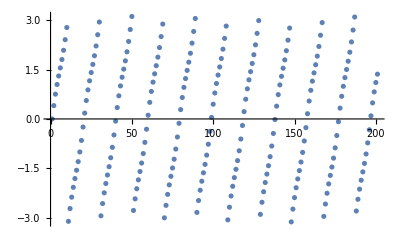

```mathematica
keep[[as,3,5]]//ListPlot
```

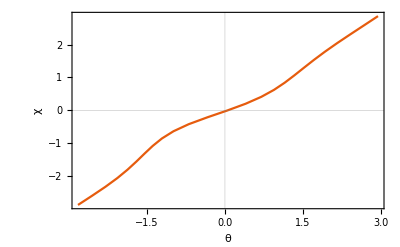

```mathematica
as=1;j=5;{t1,t2}=Transpose[{{12,29},{11,30},{11,30},{11,30},{12,30},{12,31},{12,31},{12,32},{12,33},{13,34},{13,35},{13,36},{14,37},{15,39},{15,42},{17,44},{18,48},{19,53},{22,60},{26,72}}];
ListLinePlot[Table[Transpose[{Mod[keep⟦as,j,5,t1⟦j⟧;;t2⟦j⟧⟧+π,2π]-π,π-Mod[keep⟦as,j,8,t1⟦j⟧;;t2⟦j⟧⟧+π,2 π]}],{j,14,14}],PlotTheme->"Scientific",LabelStyle->{Black,Bold,15},FrameLabel->{"θ","χ"}]
```

```mathematica
chira=ArrayReshape[Table[Transpose[{keep⟦as,j,6,t1⟦j⟧;;t2⟦j⟧⟧,Mod[keep⟦as,j,5,t1⟦j⟧;;t2⟦j⟧⟧+π,2π]-π,π-Mod[keep⟦as,j,8,t1⟦j⟧;;t2⟦j⟧⟧+π,2 π]}],{j,1,19}],{Sum[Dimensions[chira[[j]]][[1]],{j,Length[chira]}],3}];
```

```mathematica
ListPointPlot3D[Table[Transpose[{keep⟦as,j,6,t1⟦j⟧;;t2⟦j⟧⟧,Mod[keep⟦as,j,5,t1⟦j⟧;;t2⟦j⟧⟧+π,2π]-π,π-Mod[keep⟦as,j,8,t1⟦j⟧;;t2⟦j⟧⟧+π,2 π]}],{j,1,19}],PlotTheme->"Scientific",LabelStyle->{Black,Bold,15},AxesLabel->{"θ","χ"}]
```

-Graphics3D-

```mathematica
χ=Table[Transpose[{keep⟦as,j,3⟧,keep⟦as,j,4⟧,Mod[keep⟦as,j,8⟧,2π]}],{j,20}];
χ1={χ[[All,All,1]]//Flatten,χ[[All,All,2]]//Flatten,χ[[All,All,3]]//Flatten}//Transpose;chichi=χ1//Interpolation;ListPointPlot3D[χ]
ListPointPlot3D[χ1,PlotTheme->"Scientific",AxesLabel->{"R","Z","χ"},LabelStyle->{Black,Bold,15},ImageSize->300]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

-Graphics3D-

-Graphics3D-

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[…]

```mathematica
ListPointPlot3D[Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],chichi[Flatten[R⟦as⟧],Flatten[Z⟦as⟧]]}],PlotTheme->"Scientific",AxesLabel->{"R","Z","χ"},LabelStyle->{Black,Bold,15},ImageSize->300,PlotRange->{{RLEFT⟦as⟧,RLEFT⟦as⟧+0.9RDIM⟦as⟧},{-ZDIM⟦as⟧/2,ZDIM⟦as⟧/2}}]
```

InterpolatingFunction::femdmval: Input value {0.651738,-0.388857} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.651738,-0.382781} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.651738,-0.376705} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[chichi[r,z],{r,RLEFT⟦as⟧,RLEFT⟦as⟧+0.9RDIM⟦as⟧},{z,-ZDIM⟦as⟧/2,ZDIM⟦as⟧/2},RegionFunction->Function[{r,z,zz},(r-RMAXIS[[as]])^2+z^2≤2 a[[as]]^2]]
```

-Graphics3D-

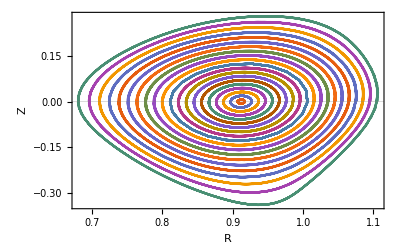

```mathematica
ListLinePlot[Table[Transpose[keep⟦1,i⟧⟦3;;4⟧],{i,Length[keep⟦1⟧]}],PlotTheme->"Scientific",LabelStyle->{Black,Bold,15},FrameLabel->{"R","Z"}]
```

```mathematica
as=1;j=3;chichi=2ArcTan[(√(RMAXIS⟦as⟧-√((keep⟦as,All,3⟧-RMAXIS⟦as⟧)^2+(keep⟦as,All,4⟧-ZMAXIS⟦as⟧)^2)))/(√(RMAXIS⟦as⟧+√((keep⟦as,All,3⟧-RMAXIS⟦as⟧)^2+(keep⟦as,All,4⟧-ZMAXIS⟦as⟧)^2)))Tan[keep[[as,All,5]]/2]];T=keep⟦as,j,2⟧;Δ=(SIBRY⟦as⟧-SIMAG⟦as⟧)/(npp-1);ψ=SIMAG⟦as⟧+Δ (Range[npp]-1);𝓆=Interpolation[Transpose[{ψ,Q⟦as⟧}]];
```

```mathematica
as=1;maxim=60;ListPlot[{keep⟦as,j,5,20;;maxim⟧,Mod[keep⟦as,j,8,20;;maxim⟧+π,2 π]-π,chichi[[j,20;;maxim]]}]
```

```mathematica
Probleme: defazajul de la R; este θ circular o aprox buna pt χ?
```

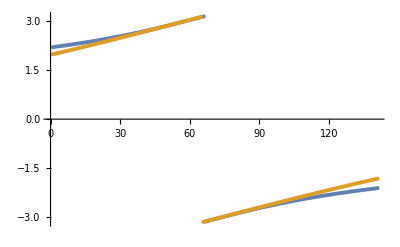

```mathematica
{t1,t2}={170,310};ListPlot[{keep⟦as,j,5,t1;;t2⟧,Mod[keep⟦as,j,8,t1;;t2⟧+π,2 π]-π}]
```

```mathematica
as=4;j=4;T=keep⟦as,j,2⟧;Δ=(SIBRY⟦as⟧-SIMAG⟦as⟧)/(npp-1);ψ=SIMAG⟦as⟧+Δ (Range[npp]-1);𝓆=Interpolation[Transpose[{ψ,Q⟦as⟧}]];
```

```mathematica
ListPlot[(keep⟦as,j,7⟧/(2 π 𝓆[keep⟦as,j,6⟧]))[[1;;2T]]]
```

```mathematica
as=24;j=10;{keep[[as,j,3]],keep[[as,j,4]],Mod[keep[[as,j,8]],2π]}//Transpose//ListPointPlot3D
```

-Graphics3D-

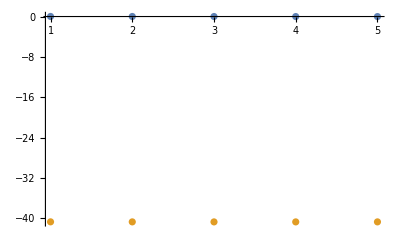

```mathematica
as=5;j=8;ListPlot[{keep⟦as,j,4,keep⟦as,j,2⟧-2;;keep⟦as,j,2⟧+2⟧,100(keep⟦as,j,3,keep⟦as,j,2⟧-2;;keep⟦as,j,2⟧+2⟧-keep⟦as,j,1⟧)},PlotRange->All]
```

```mathematica
as=4;j=13;T=keep⟦as,j,7⟧;ListPlot[keep⟦as,j,5,1;;4 T+2⟧-RotateLeft[keep⟦as,j,5,1;;4 T+2⟧]]
```

Part::span: 1;;{2,2.10882,2.21767,2.32654,2.43545,2.54442,2.65346,2.76258,«35»,6.82742,6.94599,7.06496,7.18434,7.30416,7.42441,7.5451,«1951»} is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

$Aborted[]

$Aborted

```mathematica
lex=1;ListPlot[{keep⟦as,j,6,0(2 T+lex)+1;;1 (2T+lex)⟧/keep⟦as,j,6,4(2 T+lex)+1;;5 (2T+lex)⟧}]
```

```mathematica
as=6;j=3;ListPointPlot3D[Transpose[{Flatten[Table[keep⟦as,j,2,1;;keep⟦as,j,7⟧⟧,{j,10}]],Flatten[Table[keep⟦as,j,6,1;;keep⟦as,j,7⟧⟧,{j,10}]],Flatten[Table[Mod[keep⟦as,j,5,1;;keep⟦as,j,7⟧⟧,2 π],{j,10}]]}]]
```

Part::span: 1;;{0,-0.11597,-0.22535,-0.324745,-0.412347,-0.487684,-0.551247,-0.604083,«36»,-0.326719,-0.298539,-0.269771,-0.240449,-0.210602,-0.180262,«1951»} is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1;;{0,0.0452634,0.0905174,0.1355,0.179973,0.223738,0.266639,0.308565,«35»,1.58949,1.62953,1.66977,1.71017,1.75068,1.79128,1.83193,«1951»} is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

$Aborted[]

$Aborted

Power::infy: Infinite expression 1/0. encountered.

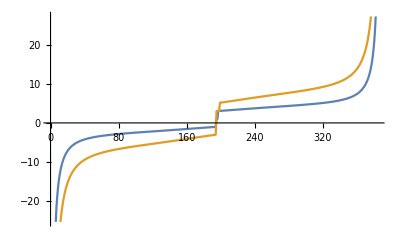

```mathematica
T=2 192;eror=0.01;ListLinePlot[{(keep⟦4,3,5,T+1;;2*T⟧-(2π+eror))/keep⟦4,3,5,1;;T⟧,(keep⟦4,3,5,2*T+1;;3*T⟧-2(2π+eror))/keep⟦4,3,5,1;;T⟧}]
```

ListPlot::lpn: 165. is not a list of numbers or pairs of numbers.

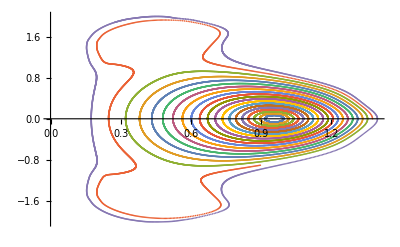
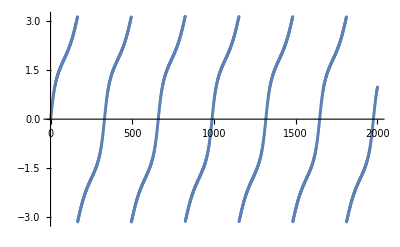
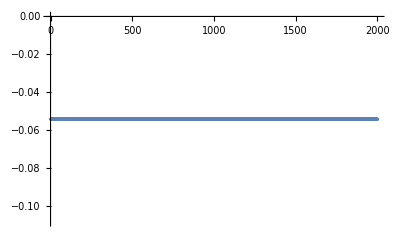
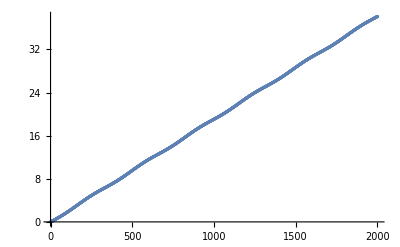
{-Graphics-,ListPlot[165],-Graphics-,-Graphics-,-Graphics-}

```mathematica
as=32;Δ=(SIBRY⟦as⟧-SIMAG⟦as⟧)/(npp-1);ψ=SIMAG⟦as⟧+Δ (Range[npp]-1);j=5;max=20;{ListPlot[Table[Transpose[keep⟦as,j,3;;4⟧],{j,max}]],ListPlot[keep⟦as,j,2⟧],ListPlot[keep⟦as,j,5⟧],ListPlot[keep⟦as,j,6⟧],ListPlot[keep⟦as,j,8⟧]}
```

```mathematica
as=4;j=4;max=2 keep⟦as,j,7⟧;max=1980;ListPlot[Transpose[{keep⟦as,j,6,1;;max⟧,keep⟦as,j,5,1;;max⟧/2/π}]]
max=18;ListPlot[{Transpose[{keep⟦as,1;;max,2,2⟧,Table[keep⟦as,j,8,2 keep⟦as,j,7⟧⟧,{j,1,max}]/(2 π)}],Transpose[{ψ,Q⟦as⟧}]}]
```

```mathematica
{r00,T,ℛ,𝒵,θ,𝒴,qbar,ν}
```

```mathematica
dorχ2=Transpose[{Flatten[Table[keep⟦as,i,3⟧,{i,max}]],Flatten[Table[keep⟦as,i,4⟧,{i,max}]],Flatten[Table[Mod[keep⟦as,i,5⟧,2π],{i,max}]]}];χ=dorχ2//Interpolation
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[{{0.31884, 1.31117}, {-1.01865, 1.01676}}, <>]

```mathematica
ListPointPlot3D[dorχ2]
```

-Graphics3D-

```mathematica
max=5;le=1;dorχ2=Transpose[{Flatten[Table[keep⟦as,i,3⟧,{i,max}]],Flatten[Table[keep⟦as,i,4⟧,{i,max}]],Flatten[Table[Mod[keep⟦as,i,5⟧,2π],{i,max}]]}];
dorχ=Transpose[{Flatten[Table[keep⟦as,i,3,1;;2 (keep⟦as,i,7⟧+le)⟧,{i,max}]],Flatten[Table[keep⟦as,i,4,1;;2 (keep⟦as,i,7⟧+le)⟧,{i,max}]],Flatten[Table[keep⟦as,i,5,1;;2 (keep⟦as,i,7⟧+le)⟧,{i,max}]]}];
```

Part::span: 1;;{2,1.92872,1.85736,1.78776,1.72295,1.6656,1.61591,1.57372,«35»,2.11162,2.15242,2.19426,2.23712,2.281,2.32589,2.3718,«1951»} is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

$Aborted[]

```mathematica
{dorχ2,dorχ}//ListPointPlot3D
```

```mathematica
as=7;Clear[fnc];Ψ=Interpolation[Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[PSI⟦as⟧]}],InterpolationOrder->order];max=18;le=0;χ=Interpolation[Transpose[{Flatten[Table[keep⟦as,i,3,1;;2 (keep⟦as,i,7⟧+le)⟧,{i,max}]],Flatten[Table[keep⟦as,i,4,1;;2 (keep⟦as,i,7⟧+le)⟧,{i,max}]],Flatten[Table[keep⟦as,i,5,1;;2 (keep⟦as,i,7⟧+le)⟧,{i,max}]]}]];{minR,maxR,minZ,maxZ}={Min[rbound⟦as⟧],Max[rbound⟦as⟧],Min[zbound⟦as⟧],Max[zbound⟦as⟧]};ngrid=100;ℛ=Transpose[Table[minR+((maxR-minR) (Range[ngrid]-1))/(ngrid-1),{j,ngrid}]];𝒵=Table[minZ+((-2minZ) (Range[ngrid]-1))/(ngrid-1),{j,ngrid}];fnc[r_,z_]=Ψ[r,z];
psihalf=fnc[RMAXIS[[as]]+a[[as]]/2,0];
ψ0=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ψ[r,z], r];ψr=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ψ[r,z], z];ψz=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ψ[r,z], r,r];ψrr=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ψ[r,z], r,z];ψrz=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ψ[r,z], z,z];ψzz=fnc[ℛ,𝒵];Δ=(SIBRY⟦as⟧-SIMAG⟦as⟧)/(npp-1);ψ=SIMAG⟦as⟧+Δ (Range[npp]-1);fnc=Interpolation[Transpose[{ψ,PRES⟦as⟧}],InterpolationOrder->order];pres=fnc[psihalf];
fnc=Interpolation[Transpose[{ψ,PPRIME⟦as⟧}],InterpolationOrder->order];
ppres=fnc[psihalf];
fnc=Interpolation[Transpose[{ψ,FPOL⟦as⟧}],InterpolationOrder->order];ℱs=fnc[ψ0];fnc=Interpolation[Transpose[{ψ,FFPRIM⟦as⟧}],InterpolationOrder->order];Fψprim=fnc[ψ0];fnc=Interpolation[Transpose[{ψ,Q⟦as⟧}],InterpolationOrder->order];qψ=fnc[ψ0];fnc2[φ34_]=D[fnc[φ34], φ34];qprim=fnc2[ψ0];chi=χ[ℛ,𝒵];chir=(RotateLeft[chi,{1,0}]-RotateLeft[chi,{-1,0}])/((2 (maxR-minR))/(ngrid-1));
chiz=(RotateLeft[chi,{0,1}]-RotateLeft[chi,{0,-1}])/((2 (maxZ-minZ))/(ngrid-1));
chir⟦All,50⟧=chir⟦All,51⟧;chiz⟦All,51⟧=chiz⟦All,50⟧;chiz⟦All,49⟧=chiz⟦All,48⟧;
```

Part::span: 1;;{0,1.57705,3.07982,4.4587,5.68695,6.75865,7.68207,8.47275,«35»,13.6473,13.663,13.681,13.7019,13.7258,13.7531,13.784,«1951»} is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1;;{0,0.166762,0.334174,0.502677,0.672511,0.843691,1.01602,1.18913,«35»,5.0169,5.09344,5.17478,5.26171,5.35448,5.45331,5.55831,«1951»} is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

$Aborted[]

```mathematica
{Transpose[{ℛ//Flatten,𝒵//Flatten,chi//Flatten}]//ListPointPlot3D,Transpose[{ℛ//Flatten,𝒵//Flatten,chir//Flatten}]//ListPointPlot3D,Transpose[{ℛ//Flatten,𝒵//Flatten,chiz//Flatten}]//ListPointPlot3D}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Transpose[{ℛ//Flatten,𝒵//Flatten,chir//Flatten}]//ListPointPlot3D
```

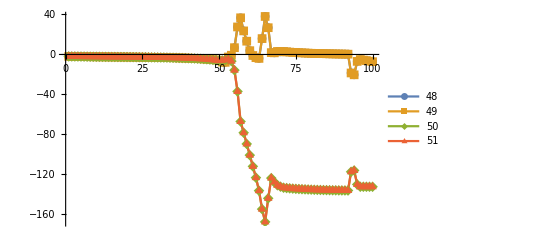

```mathematica
ListPlot[{chiz⟦All,48⟧,chiz⟦All,49⟧,chiz⟦All,50⟧,chiz⟦All,51⟧},PlotRange->All,Joined->True,PlotMarkers->Automatic,PlotLegends->{48,49,50,51,52}]
```

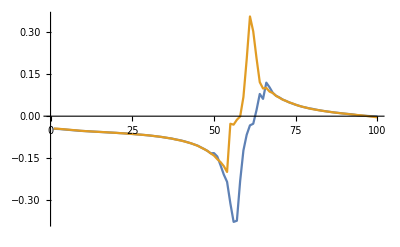

```mathematica
{i1,i2}={48,53};ListLinePlot[{chi⟦All,i1⟧-chi⟦All,i1-1⟧,chi⟦All,i2+1⟧-chi⟦All,i2⟧},Joined->True,PlotRange->{All,All}]
```

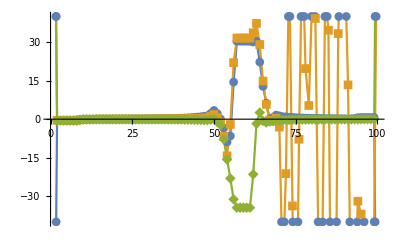

```mathematica
ListPlot[{chir⟦All,49⟧,chir⟦All,50⟧,chir⟦All,51⟧},Joined->True,PlotMarkers->Automatic,PlotRange->{All,{-40,40}}]
```

```mathematica
ListPointPlot3D[chir,PlotRange->{{40,60},{0,100},{-40,40}}]
```

-Graphics3D-

```mathematica
Clear[F];Monitor[For[as=1,as≤Length[data4],as++,order=4;
Clear[fnc];Ψ=Interpolation[Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[PSI⟦as⟧]}],InterpolationOrder->order];max=18;le=0;χ=Interpolation[Transpose[{Flatten[Table[keep⟦as,i,3,1;;2 (keep⟦as,i,7⟧+le)⟧,{i,max}]],Flatten[Table[keep⟦as,i,4,1;;2 (keep⟦as,i,7⟧+le)⟧,{i,max}]],Flatten[Table[keep⟦as,i,5,1;;2 (keep⟦as,i,7⟧+le)⟧,{i,max}]]}]];{minR,maxR,minZ,maxZ}={Min[rbound⟦as⟧],Max[rbound⟦as⟧],Min[zbound⟦as⟧],Max[zbound⟦as⟧]};ngrid=100;ℛ=Transpose[Table[minR+((maxR-minR) (Range[ngrid]-1))/(ngrid-1),{j,ngrid}]];𝒵=Table[minZ+((-2minZ) (Range[ngrid]-1))/(ngrid-1),{j,ngrid}];fnc[r_,z_]=Ψ[r,z];
psihalf=fnc[RMAXIS[[as]]+a[[as]]/2,0];
ψ0=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ψ[r,z], r];ψr=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ψ[r,z], z];ψz=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ψ[r,z], r,r];ψrr=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ψ[r,z], r,z];ψrz=fnc[ℛ,𝒵];fnc[r_,z_]=D[Ψ[r,z], z,z];ψzz=fnc[ℛ,𝒵];Δ=(SIBRY⟦as⟧-SIMAG⟦as⟧)/(npp-1);ψ=SIMAG⟦as⟧+Δ (Range[npp]-1);fnc=Interpolation[Transpose[{ψ,PRES⟦as⟧}],InterpolationOrder->order];pres=fnc[psihalf];
fnc=Interpolation[Transpose[{ψ,PPRIME⟦as⟧}],InterpolationOrder->order];
ppres=fnc[psihalf];
fnc=Interpolation[Transpose[{ψ,FPOL⟦as⟧}],InterpolationOrder->order];ℱs=fnc[ψ0];fnc=Interpolation[Transpose[{ψ,FFPRIM⟦as⟧}],InterpolationOrder->order];Fψprim=fnc[ψ0];fnc=Interpolation[Transpose[{ψ,Q⟦as⟧}],InterpolationOrder->order];qψ=fnc[ψ0];fnc2[φ34_]=D[fnc[φ34], φ34];qprim=fnc2[ψ0];chi=χ[ℛ,𝒵];chir=(RotateLeft[chi,{1,0}]-RotateLeft[chi,{-1,0}])/((2 (maxR-minR))/(ngrid-1));
chiz=(RotateLeft[chi,{0,1}]-RotateLeft[chi,{0,-1}])/((2 (maxZ-minZ))/(ngrid-1));
chir⟦All,50⟧=chir⟦All,51⟧;chiz⟦All,51⟧=chiz⟦All,50⟧;chiz⟦All,49⟧=chiz⟦All,48⟧;

QQ=Flatten[{R0⟦as⟧,B0⟦as⟧,ngrid,ngrid,minR,maxR,minZ,maxZ,pres,ppres,a⟦as⟧,δ⟦as⟧,κ⟦as⟧,Flatten[ψ0],Flatten[ψr],Flatten[ψz],Flatten[ψrr],Flatten[ψrz],Flatten[ψzz],Flatten[ℱs],Flatten[Fψprim],Flatten[qψ],Flatten[qprim],Flatten[chi],Flatten[chir],Flatten[chiz]}];Export[folderdata<>"\\QQ"<>StringTake[files⟦as⟧,-8],QQ];],as]
```

## Analytical calculus

```mathematica
Clear["`*"]
```

```mathematica
B=F[ψ]∇ζ+∇ζ x ∇ψ = F[ψ]Subscript[e, ζ]/R+1/R D[ψ, R] Subscript[e, ζ] x Subscript[e, R]+1/R D[ψ, Z] Subscript[e, ζ] x Subscript[e, Z];
B=F[ψ]Subscript[e, ζ]/R-1/R D[ψ, R] Subscript[e, Z]+1/R D[ψ, Z] Subscript[e, R];
B^2=(F^2+D[ψ^2, R]+D[ψ^2, Z])/R^2;
B1=B.∇R=1/R D[ψ, Z];
B2=B.∇(R0 ζ)=R0/R^2 F;
B3=B.∇Z=-1/R D[ψ, R];
∇ x b = ∇ x B/Bn = (∇ x B)/Bn -  ∇Bn x B/Bn^2;
∇Bn = D[Bn, R] Subscript[e, R]+  D[Bn, Z] Subscript[e, Z];
∇Bn x B = (D[Bn, R] Subscript[e, R]+D[Bn, Z] Subscript[e, Z])x (F[ψ]Subscript[e, ζ]/R-1/R D[ψ, R] Subscript[e, Z]+1/R D[ψ, Z] Subscript[e, R]) = D[Bn, R] F[ψ]Subscript[e, Z]/R + D[Bn, R] 1/R D[ψ, R] Subscript[e, ζ]-D[Bn, Z] F[ψ]Subscript[e, R]/R+D[Bn, Z] 1/R D[ψ, Z] Subscript[e, ζ] = F[ψ]/R(D[Bn, R] Subscript[e, Z]-D[Bn, Z] Subscript[e, R])+ (D[Bn, R]  D[ψ, R]+D[Bn, Z]  D[ψ, Z]) Subscript[e, ζ]/R
```

```mathematica
Curl[{1/R D[ψ[R,Z], Z],F[ψ[R,Z]]/R,-1/R D[ψ[R,Z], R]},{R,ζ,Z}]
```

{-(F'[ψ[R,Z]] ψ^(0,1)[R,Z])/R,(ψ^(0,2)[R,Z])/R-(ψ^(1,0)[R,Z])/R^2+(ψ^(2,0)[R,Z])/R,-F[ψ[R,Z]]/R^2+(F'[ψ[R,Z]] ψ^(1,0)[R,Z])/R}

```mathematica
θ=ArcTan[R-R0,Z-Z0];
```

((-Z+Z0) ψ^(0,1)[R,Z])/(R ((R-R0)^2+(Z-Z0)^2))-((R-R0) ψ^(1,0)[R,Z])/(R ((R-R0)^2+(Z-Z0)^2))

```mathematica
B[R,Z].Grad[ζ,{R,ζ,Z},"Cylindrical"]/B[R,Z].Grad[θ,{R,ζ,Z},"Cylindrical"]//FullSimplify
```

-(((R-R0)^2+(Z-Z0)^2) F[ψ[R,Z]])/(R (Z-Z0) ψ^(0,1)[R,Z]+R (R-R0) ψ^(1,0)[R,Z])

```mathematica
B[R_,Z_]=F[ψ[R,Z]]Grad[ζ,{R,ζ,Z},"Cylindrical"]+Cross[Grad[ζ,{R,ζ,Z},"Cylindrical"],Grad[ψ[R,Z],{R,ζ,Z},"Cylindrical"]];
Sqrt[B[R,Z].B[R,Z]]Curl[B[R,Z]/Sqrt[B[R,Z].B[R,Z]],{R,ζ,Z},"Cylindrical"]//FullSimplify
```

{(-F'[ψ[R,Z]] ψ^(0,1)[R,Z] ((ψ^(0,1)[R,Z])^2+(ψ^(1,0)[R,Z])^2)+F[ψ[R,Z]] (ψ^(0,1)[R,Z] ψ^(0,2)[R,Z]+ψ^(1,0)[R,Z] ψ^(1,1)[R,Z]))/(R (F[ψ[R,Z]]^2+(ψ^(0,1)[R,Z])^2+(ψ^(1,0)[R,Z])^2)),(ψ^(0,2)[R,Z] (ψ^(1,0)[R,Z])^2-F[ψ[R,Z]] F'[ψ[R,Z]] ((ψ^(0,1)[R,Z])^2+(ψ^(1,0)[R,Z])^2)+F[ψ[R,Z]]^2 (ψ^(0,2)[R,Z]+ψ^(2,0)[R,Z])+ψ^(0,1)[R,Z] (-2 ψ^(1,0)[R,Z] ψ^(1,1)[R,Z]+ψ^(0,1)[R,Z] ψ^(2,0)[R,Z]))/(R (F[ψ[R,Z]]^2+(ψ^(0,1)[R,Z])^2+(ψ^(1,0)[R,Z])^2)),(F[ψ[R,Z]]^3+R F'[ψ[R,Z]] ψ^(1,0)[R,Z] ((ψ^(0,1)[R,Z])^2+(ψ^(1,0)[R,Z])^2)+F[ψ[R,Z]] ((ψ^(0,1)[R,Z])^2-R ψ^(0,1)[R,Z] ψ^(1,1)[R,Z]+ψ^(1,0)[R,Z] (ψ^(1,0)[R,Z]-R ψ^(2,0)[R,Z])))/(R^2 (F[ψ[R,Z]]^2+(ψ^(0,1)[R,Z])^2+(ψ^(1,0)[R,Z])^2))}

```mathematica
Curl[{B1[R,Z],B2[R,Z],B3[R,Z]},{R,ζ,Z},"Cylindrical"]
```

{-B2^(0,1)[R,Z],B1^(0,1)[R,Z]-B3^(1,0)[R,Z],B2[R,Z]/R+B2^(1,0)[R,Z]}

```mathematica
B[R_,Z_]={B1[R,Z],B2[R,Z],B3[R,Z]};b[R_,Z_]=B[R,Z]/Bm[R,Z];Curl[b[R,Z],{R,ζ,Z},"Cylindrical"]
```

{-(B2^(0,1)[R,Z])/Bm[R,Z]+(B2[R,Z] Bm^(0,1)[R,Z])/Bm[R,Z]^2,(B1^(0,1)[R,Z])/Bm[R,Z]-(B1[R,Z] Bm^(0,1)[R,Z])/Bm[R,Z]^2-(B3^(1,0)[R,Z])/Bm[R,Z]+(B3[R,Z] Bm^(1,0)[R,Z])/Bm[R,Z]^2,B2[R,Z]/(R Bm[R,Z])+(B2^(1,0)[R,Z])/Bm[R,Z]-(B2[R,Z] Bm^(1,0)[R,Z])/Bm[R,Z]^2}

```mathematica
F∇ξ+∇ξ x∇ψ=∇y x ∇ ψ->F∇ξ=∇y2 x ∇ ψ->F∇ξ=D[y2, r]∇r x ∇ ψ+D[y2, z]∇z x ∇ ψ->;
F∇ξ ∇ξ=D[y2, r](∇r x ∇ ψ)∇ξ+D[y2, z](∇z x ∇ ψ)∇ξ->F(∇ξ)^2 R=-D[y2, r]D[ψ, z]+D[y2, z]D[ψ, r]
```

```mathematica
F/R=-D[y2, r]D[ψ, z]+D[y2, z]D[ψ, r];
z=0->D[ψ, z]=0->F/R=D[y2, z]D[ψ, r](z=0)->F(r,0)/r/D[ψ, r](r,z)=D[y2, z](r,0)
```

```mathematica
F/R=-D[y2, r]D[ψ, z]+D[y2, z]D[ψ, r];
```

```mathematica
Cross[Grad[ζ,{R,ζ,Z},"Cylindrical"],Grad[ψ[R,Z],{R,ζ,Z},"Cylindrical"]].Cross[Grad[ζ,{R,ζ,Z},"Cylindrical"],Grad[ψ[R,Z],{R,ζ,Z},"Cylindrical"]]
```

((ψ^(0,1)[R,Z])^2)/R^2+((ψ^(1,0)[R,Z])^2)/R^2

```mathematica
(Grad[ζ,{R,ζ,Z},"Cylindrical"].Grad[ζ,{R,ζ,Z},"Cylindrical"])(Grad[ψ[R,Z],{R,ζ,Z},"Cylindrical"].Grad[ψ[R,Z],{R,ζ,Z},"Cylindrical"])
```

((ψ^(0,1)[R,Z])^2+(ψ^(1,0)[R,Z])^2)/R^2

```mathematica
Clear["`*"]
```

```mathematica
(*real vs s-α field*)
```

```mathematica
B=∇χ x ∇θ+∇ζ x∇ψ=q(ψ)∇ψ x ∇θ+∇ζ x∇ψ;
Bpol=(∇ζ x∇ψ).∇θ
Btor=q(ψ)(∇ψ x∇θ).∇ζ
B=∇y x ∇ψ=∇(ζ-q θ) x ∇ψ = q∇ψ x ∇θ +∇ζ x ∇ψ ;
Btoroidalfals=q(ψ)(∇ψ x ∇θ).∇ζ=q(ψ)Btorreal/Subscript[q, θ](ψ,θ)=Btorreal q(ψ)/Subscript[q, θ](ψ,θ)
```

```mathematica
(*going to cylindrical*)
```

```mathematica
r=Sqrt[Z^2+(R-R0)^2];θ=ArcTan[R-R0,Z];
hr=1/Sqrt[Grad[r,{R,ζ,Z},"Cylindrical"].Grad[r,{R,ζ,Z},"Cylindrical"]//FullSimplify];hθ=1/Sqrt[Grad[θ,{R,ζ,Z},"Cylindrical"].Grad[θ,{R,ζ,Z},"Cylindrical"]//FullSimplify];hζ=1/Sqrt[Grad[ζ,{R,ζ,Z},"Cylindrical"].Grad[ζ,{R,ζ,Z},"Cylindrical"]//FullSimplify];
eθ=Grad[θ,{R,ζ,Z},"Cylindrical"]hθ;
eζ=Grad[ζ,{R,ζ,Z},"Cylindrical"]hζ;
er=Grad[r,{R,ζ,Z},"Cylindrical"]hr;
B=F[ψ[R,Z]]Grad[ζ,{R,ζ,Z},"Cylindrical"]+Cross[Grad[ζ,{R,ζ,Z},"Cylindrical"],Grad[ψ[R,Z],{R,ζ,Z},"Cylindrical"]];
```

```mathematica
Grad[θ,{R,ζ,Z},"Cylindrical"].Grad[ψ[R,Z],{R,ζ,Z},"Cylindrical"]
```

((R-R0) ψ^(0,1)[R,Z])/((R-R0)^2+Z^2)-(Z ψ^(1,0)[R,Z])/((R-R0)^2+Z^2)

```mathematica
Btor
```

F[ψ[R,Z]]/R^2

```mathematica
Btor/Bpol//FullSimplify
```

-(((R-R0)^2+Z^2) F[ψ[R,Z]])/(R Z ψ^(0,1)[R,Z]+R (R-R0) ψ^(1,0)[R,Z])

```mathematica
Btor=B.Grad[ζ,{R,ζ,Z},"Cylindrical"];
Bpol=B.Grad[θ,{R,ζ,Z},"Cylindrical"]//FullSimplify;
Btor2=B.eζ;
Bpol2=B.eθ;
```

```mathematica
(B-Btor eζ hζ-Bpol eθ hθ)//FullSimplify
```

{((R-R0) ((R-R0) ψ^(0,1)[R,Z]-Z ψ^(1,0)[R,Z]))/(R ((R-R0)^2+Z^2)),0,(Z ((R-R0) ψ^(0,1)[R,Z]-Z ψ^(1,0)[R,Z]))/(R ((R-R0)^2+Z^2))}

```mathematica
B-Btor2 eζ-Bpol2 eθ//FullSimplify
```

{((R-R0) ((R-R0) ψ^(0,1)[R,Z]-Z ψ^(1,0)[R,Z]))/(R ((R-R0)^2+Z^2)),0,(Z ((R-R0) ψ^(0,1)[R,Z]-Z ψ^(1,0)[R,Z]))/(R ((R-R0)^2+Z^2))}

```mathematica
B.B
```

F[ψ[R,Z]]^2/R^2+((ψ^(0,1)[R,Z])^2)/R^2+((ψ^(1,0)[R,Z])^2)/R^2

```mathematica
Btor2^2+Bpol^2//FullSimplify
```

(F[ψ[R,Z]]^2+((Z ψ^(0,1)[R,Z]+(R-R0) ψ^(1,0)[R,Z])^2)/(((R-R0)^2+Z^2)^2))/R^2

```mathematica
(Btor R)^2+(Bpol)^2((R-R0)^2+Z^2)//FullSimplify
```

```mathematica
(2Z (Derivative[0,1][ψ][R,Z])(R-R0)( Derivative[1,0][ψ][R,Z])+Z^2 (Derivative[0,1][ψ][R,Z])^2+(R-R0)^2( Derivative[1,0][ψ][R,Z])^2)/((R-R0)^2+Z^2)
```

```mathematica
-( Derivative[1,0][ψ][R,Z](Z)-(R-R0) (Derivative[0,1][ψ][R,Z]))/((R-R0)^2+Z^2)
```

```mathematica
B.B//FullSimplify
```

(F[ψ[R,Z]]^2+(ψ^(0,1)[R,Z])^2+(ψ^(1,0)[R,Z])^2)/R^2

```mathematica
B=F ∇ζ+∇ζ x∇ψ->;
Bpol=(∇ζ x∇ψ)∇θ=D[ψ, ρ](∇ζ x∇ ρ)∇θ+D[ψ, z](∇ζ x∇ z)∇θ;
Bpol=D[ψ, ρ]D[θ, ρ](∇ζ x∇ ρ)∇ρ+D[ψ, ρ]D[θ, z](∇ζ x∇ ρ)∇z+D[ψ, z]D[θ, z](∇ζ x∇ z)∇z+D[ψ, z]D[θ, ρ](∇ζ x∇ z)∇ρ;
Bpol=(-D[ψ, ρ]D[θ, z]+D[ψ, z]D[θ, ρ])/ρ=-(D[ψ, ρ](-R0+ρ)+D[ψ, z] z)/ρ/(z^2+(-R0+ρ)^2);
Btor=F(∇ζ)^2=F[ψ]/ρ^2;
```

```mathematica
B=(B.∇ζ)Subscript[e, ζ]+(B.∇θ)Subscript[e, θ]
```

```mathematica
B^2=(B.∇ζ)^2 Subscript[h, ζ]^2+(B.∇θ)Subscript[h, θ]^2
```

$Aborted[]

```mathematica
F ∇ζ+∇ζ x ∇ψ=∇y x ∇ψ->F ∇ζ=∇(y-ζ) x ∇ψ->F ∇ζ=∇y2 x ∇ψ->
```

```mathematica
F ∇ζ=D[y2, r]∇r x ∇ψ+D[y2, z]∇z x ∇ψ+D[y2, ζ]∇ζ x ∇ψ
```

```mathematica
F ∇ζ=D[y2, r]D[ψ, z]∇r x ∇z+D[y2, z]D[ψ, r]∇z x ∇r+D[y2, ζ]D[ψ, z]∇ζ x ∇z+D[y2, ζ]D[ψ, r]∇ζ x ∇r
```

```mathematica
(*here*)
```

```mathematica
F ∇ζ.∇ζ=D[y2, r]D[ψ, z]∇r x ∇z.∇ζ+D[y2, z]D[ψ, r]∇z x ∇r.∇ζ
```

```mathematica
F |∇ζ|=D[y2, r]D[ψ, z](-1)+D[y2, z]D[ψ, r](+1)
```

```mathematica
∇y2 x ∇ψ = F∇ζ->F |∇ζ|=D[y2, r]D[ψ, z](-1)+D[y2, z]D[ψ, r](+1)
```

```mathematica
∇y2⊥∇ψ -> (D[y2, r] ∇r+D[y2, z] ∇z) .(D[ψ, r] ∇r+D[ψ, z] ∇z) = 0->(D[y2, r]D[ψ, r]+D[y2, z] D[ψ, z])= 0
```

```mathematica
∇y2 = FF/|∇ψ|^2(ez x∇ψ)
```

```mathematica
{∂_r ψ,∂_z ψ}{∂_r y2,D[y2, z]}=0
{-∂_z ψ,∂_r ψ}{∂_r y2,D[y2, z]}=F|∇ζ|
```

Part::partd: Part specification «1» is longer than depth of object.

Part::pkspec1: The expression 50.2655/({«1»}⟦12,10,7⟧) cannot be used as a part specification.

$Aborted[]

```mathematica
(*Scaling data::
Space with R0 = RMAXIS; B0 = BMAXIS, not BCENTR!!!; Pressure with B0^2/μ0=magnetic pressure.
*)

R0=RCENTR;
B0=BCENTR;

R0=RMAXIS;
B0=FPOL[[All,1]]/RMAXIS;


RDIM=Table[RDIM[[i]]/R0[[i]],{i,Length[data4]}];
ZDIM=Table[ZDIM[[i]]/R0[[i]],{i,Length[data4]}];
RLEFT=Table[RLEFT[[i]]/R0[[i]],{i,Length[data4]}];
RCENTR=Table[RCENTR[[i]]/R0[[i]],{i,Length[data4]}];
BCENTR=Table[BCENTR[[i]]/B0[[i]],{i,Length[data4]}];
RMAXIS=Table[RMAXIS[[i]]/R0[[i]],{i,Length[data4]}];
ZMAXIS=Table[ZMAXIS[[i]]/R0[[i]],{i,Length[data4]}];
SIMAG=Table[SIMAG[[i]]/R0[[i]]^2/B0[[i]],{i,Length[data4]}];
SIBRY=Table[SIBRY[[i]]/R0[[i]]^2/B0[[i]],{i,Length[data4]}];
R=Table[R[[i]]/R0[[i]],{i,Length[data4]}];
Z=Table[Z[[i]]/R0[[i]],{i,Length[data4]}];
δR=Table[δR[[i]]/R0[[i]],{i,Length[data4]}];
δZ=Table[δZ[[i]]/R0[[i]],{i,Length[data4]}];
PSI=Table[PSI[[i]]/R0[[i]]^2/B0[[i]],{i,Length[data4]}];
PSIR=Table[PSIR[[i]]/R0[[i]]/B0[[i]],{i,Length[data4]}];
PSIZ=Table[PSIZ[[i]]/R0[[i]]/B0[[i]],{i,Length[data4]}];
PSIRR=Table[PSIRR[[i]]/B0[[i]],{i,Length[data4]}];
PSIRZ=Table[PSIRZ[[i]]/B0[[i]],{i,Length[data4]}];
PSIZZ=Table[PSIZZ[[i]]/B0[[i]],{i,Length[data4]}];


FPOL=Table[FPOL[[i]]/R0[[i]]/B0[[i]],{i,Length[data4]}];
PRES=Table[PRES[[i]],{i,Length[data4]}];
FFPRIM=Table[FFPRIM[[i]]/(B0[[i]])^1,{i,Length[data4]}];
PPRIME=Table[PPRIME[[i]](B0[[i]] R0[[i]]^2)^1,{i,Length[data4]}];
rlim=Table[rlim[[i]]/R0[[i]],{i,Length[data4]}];
zlim=Table[zlim[[i]]/R0[[i]],{i,Length[data4]}];
rbound=Table[rbound[[i]]/R0[[i]],{i,Length[data4]}];
zbound=Table[zbound[[i]]/R0[[i]],{i,Length[data4]}];
```